```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
data=Import["data_with_time_windows2.mx"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

Width Feature

```mathematica
window=10;
rawaim=data[[window]][[All,9]];
pos=Partition[Flatten@Table[Position[rawaim,i],{i,{"NA",0}}],1];
```

```mathematica
aim=Delete[rawaim,pos];
```

```mathematica
campaign=Delete[data[[window]][[All,2]],pos];
```

```mathematica
seri=Delete[data[[window]][[All,1]],pos];
```

```mathematica
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {145}

aim data length: {397873}

sequence data groups amount: {676}

```mathematica
Print["bucket size: ",bucketsize=Ceiling@(N@(Dimensions@aim)/55)]
aimlabeled=Thread[Range@Length@aim->aim];
aimpartitioned=Partition[Normal@Sort@Association@aimlabeled,UpTo@bucketsize];
bins=Table[MinMax[i],{i,Values@aimpartitioned}];
Print["node amount: ",Length@bins];
```

bucket size: {7235}

node amount: 55

```mathematica
Tally@bins
```

{{{915.,992.},1},{{992.,1080.},1},{{1080.,1130.},1},{{1130.,1180.},1},{{1180.,1200.},1},{{1200.,1210.},1},{{1210.,1220.},1},{{1220.,1220.},2},{{1220.,1230.},1},{{1230.,1240.},1},{{1240.,1250.},1},{{1250.,1260.},1},{{1260.,1260.},2},{{1260.,1270.},1},{{1270.,1270.},1},{{1270.,1290.},1},{{1290.,1310.},1},{{1310.,1330.},1},{{1330.,1360.},1},{{1360.,1390.},1},{{1390.,1400.},1},{{1400.,1430.},1},{{1430.,1450.},1},{{1450.,1490.},1},{{1490.,1520.},1},{{1520.,1520.},1},{{1520.,1530.},1},{{1530.,1530.},4},{{1530.,1540.},1},{{1540.,1540.},3},{{1540.,1550.},1},{{1550.,1560.},1},{{1560.,1570.},1},{{1570.,1580.},1},{{1580.,1590.},1},{{1590.,1620.},1},{{1620.,1690.},1},{{1690.,1770.},1},{{1770.,1800.},1},{{1800.,1830.},1},{{1830.,1840.},1},{{1840.,1840.},1},{{1840.,1850.},1},{{1850.,1850.},2},{{1850.,1860.},1},{{1860.,1870.},1},{{1870.,9930.},1}}

```mathematica
repetitivesreport=DeleteCases[Tally@bins,x_/;x[[2]]==1];
repetitives=repetitivesreport[[All,1]];
labelgeneration[x_]:=Table[{repetitives[[x]][[1]]+i*repetitives[[x]][[1]]/10^(RealDigits@repetitives[[x]][[1]])[[2]],repetitives[[x]][[2]]+i*repetitives[[x]][[2]]/10^(RealDigits@repetitives[[x]][[2]])[[2]]},{i,Range@repetitivesreport[[x]][[2]]}]
binsrearranged=ReplacePart[bins,Flatten[Table[MapThread[#1->#2&,{Flatten@Position[bins,repetitives[[g]]],labelgeneration[g]}],{g,Range@Length@repetitives}],1]];
```

```mathematica
aimbinned=Values@Normal@KeySort@Association@Flatten[Table[aimpartitioned[[i]]/.Table[Values@aimpartitioned[[i]][[j]]->binsrearranged[[i]],{j,Length@aimpartitioned[[i]]}],{i,Length@aimpartitioned}],1];
Position[aimbinned,Null]
```

{}

```mathematica
aim=aimbinned;
binningmembers=Sort[DeleteDuplicates[aim]];
Print["binning amount: ",Dimensions@DeleteDuplicates@aimbinned]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

binning amount: {55,2}

dimension of binned data: {397873,2}

binning members dimension : {55,2}

```mathematica
binningmembers=Sort[DeleteDuplicates[aim]]
```

{{915.,992.},{992.,1080.},{1080.,1130.},{1130.,1180.},{1180.,1200.},{1200.,1210.},{1210.,1220.},{1220.,1230.},{1220.12,1220.12},{1220.24,1220.24},{1230.,1240.},{1240.,1250.},{1250.,1260.},{1260.,1270.},{1260.13,1260.13},{1260.25,1260.25},{1270.,1270.},{1270.,1290.},{1290.,1310.},{1310.,1330.},{1330.,1360.},{1360.,1390.},{1390.,1400.},{1400.,1430.},{1430.,1450.},{1450.,1490.},{1490.,1520.},{1520.,1520.},{1520.,1530.},{1530.,1540.},{1530.15,1530.15},{1530.31,1530.31},{1530.46,1530.46},{1530.61,1530.61},{1540.,1550.},{1540.15,1540.15},{1540.31,1540.31},{1540.46,1540.46},{1550.,1560.},{1560.,1570.},{1570.,1580.},{1580.,1590.},{1590.,1620.},{1620.,1690.},{1690.,1770.},{1770.,1800.},{1800.,1830.},{1830.,1840.},{1840.,1840.},{1840.,1850.},{1850.,1860.},{1850.19,1850.19},{1850.37,1850.37},{1860.,1870.},{1870.,9930.}}

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

binning groups association to count of their total members: <|{915.,992.}→7235,{992.,1080.}→7235,{1080.,1130.}→7235,{1130.,1180.}→7235,{1180.,1200.}→7235,{1200.,1210.}→7235,{1210.,1220.}→7235,{1220.,1230.}→7235,{1220.12,1220.12}→7235,{1220.24,1220.24}→7235,{1230.,1240.}→7235,{1240.,1250.}→7235,{1250.,1260.}→7235,{1260.,1270.}→7235,{1260.13,1260.13}→7235,{1260.25,1260.25}→7235,{1270.,1270.}→7235,{1270.,1290.}→7235,{1290.,1310.}→7235,{1310.,1330.}→7235,{1330.,1360.}→7235,{1360.,1390.}→7235,{1390.,1400.}→7235,{1400.,1430.}→7235,{1430.,1450.}→7235,{1450.,1490.}→7235,{1490.,1520.}→7235,{1520.,1520.}→7235,{1520.,1530.}→7235,{1530.,1540.}→7235,{1530.15,1530.15}→7235,{1530.31,1530.31}→7235,{1530.46,1530.46}→7235,{1530.61,1530.61}→7235,{1540.,1550.}→7235,{1540.15,1540.15}→7235,{1540.31,1540.31}→7235,{1540.46,1540.46}→7235,{1550.,1560.}→7235,{1560.,1570.}→7235,{1570.,1580.}→7235,{1580.,1590.}→7235,{1590.,1620.}→7235,{1620.,1690.}→7235,{1690.,1770.}→7235,{1770.,1800.}→7235,{1800.,1830.}→7235,{1830.,1840.}→7235,{1840.,1840.}→7235,{1840.,1850.}→7235,{1850.,1860.}→7235,{1850.19,1850.19}→7235,{1850.37,1850.37}→7235,{1860.,1870.}→7235,{1870.,9930.}→7183|>

binning amount: {55,2}

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
```

{0.0781406,Null}

{55,2}

{1485,2,2}

{676}

{7.52289,Null}

```mathematica
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
```

{0.0027987,Null}

```mathematica
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

{675,2,2}

{0.163504,Null}

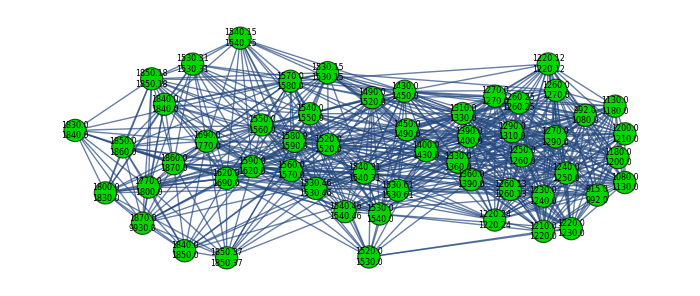

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->Automatic,DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->1,VertexStyle->RGBColor[0.02,0.84,0.],VertexLabelStyle->Directive[Black,Italic,8],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->700]
```